```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved. decoy integrated into r2, r1 self activates

 r1+r2 <-->C
t+e --> (te)b-->e
r2+e -> (r2e)^b -->e 
c+e --> (ce)b-->e+r1
	r1 self activates
*)
```

```mathematica
gT=10; (*t growth*)
gR1=1; (*NLR growth*)
gR2=1;
deltaT=1; (*t decay*)
deltaR=1; (*NLR decay*)
beta1=1; (*effector-target affinity*)
beta2=1; (*effector-target unbinding*)
```

```mathematica
(*r1-r1 binding and unbinding*)
f0=0; 
b0=1;
```

```mathematica
(*r1-r2 binding and unbinding*)
(*f1=0.5;*)
b1=1;
```

```mathematica
(*C12-e1*)
```

```mathematica
(*f2=0.5;*)
b2=1;
```

```mathematica
(*(C12e)^b-(C12e)^b*)
```

```mathematica
(*f3=0.5;*)
b3=1;
```

```mathematica
(*A and C11 to a_1*)
```

```mathematica
kappa=1;
```

```mathematica
f1=1;
f2=1;
f3=1;
```

## Equations

```mathematica
(*solve for E, C12, (C12e)^b, A based on e0 and quasi-equilibrium*)
```

```mathematica
(*d/dt C12=0*)
eq1=f1*r1Input*r2Input-b1*c12Var-f2*eVar*c12Var+b2*c12ebVar==0;
```

```mathematica
(*d/dt c12eb =0*)
eq2=f2*eVar*c12Var-b2*c12ebVar-f3*c12ebVar^2+b3*Avar==0;
```

```mathematica
(*d/dt A=0*)
eq3=f3*c12ebVar^2-b3*Avar-kappa*Avar==0;
```

```mathematica
(*Eq balance*)
```

```mathematica
eq4=eVar+(f2/b2)*r2Input*eVar+(beta1/beta2)*tInput*eVar+c12ebVar+2*Avar-e0Var==0;
```

```mathematica
fixedSol={eVar,c12Var,c12ebVar,Avar}/.Solve[{eq1,eq2,eq3,eq4},{eVar,c12Var,c12ebVar,Avar}];
getComplexes[thisR1_?NumericQ,thisR2_?NumericQ,thisT_?NumericQ,thisE0_?NumericQ]:=Module[{numericSol,final,realSol,processedSol,i,thisSol},

numericSol=fixedSol/.{r1Input->thisR1,r2Input->thisR2,tInput->thisT,e0Var->thisE0}//N;
numericSol=numericSol//Chop;
(*get real solutions*)
realSol=Cases[numericSol,{__Real}];
(*eliminate negatives*)
processedSol={};
For[i=1,i<=Length[realSol],i++,
thisSol=realSol[[i]];
If[(Min[thisSol]>=0),AppendTo[processedSol,thisSol]];
];

(*Make sure there's only one solution*)
If[Length[processedSol]==1,final=processedSol[[1]],final="error"];
final

]
```

```mathematica
(*the activating NLR*)
dr1ds[r1Var_,r2Var_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisC12,thisC12eb,thisA,z},

(*{thisE,thisC12,thisC12eb,thisA}=getComplexes[r1Var,r2Var,tVar,e0Var];*)
z=getComplexes[r1Var,r2Var,tVar,e0Var];
thisE=z[[1]];
thisC12=z[[2]];
thisC12eb=z[[3]];
thisA=z[[4]];

gR1-deltaR*r1Var-f1*r1Var*r2Var+b1*thisC12-f0*(r1Var^2)*kappa/(b0+kappa)+f[aVar]

]
```

```mathematica
dtds[r1Var_,r2Var_,tVar_,e0Var_]:=Module[{thisE,thisC12,thisC12eb,thisA,z},

(*{thisE,thisC12,thisC12eb,thisA}=getComplexes[r1Var,r2Var,tVar,e0Var];*)
z=getComplexes[r1Var,r2Var,tVar,e0Var];
thisE=z[[1]];
thisC12=z[[2]];
thisC12eb=z[[3]];
thisA=z[[4]];

gT-deltaT*tVar-beta1*tVar*thisE

]
```

```mathematica
(*the integrated-decoy NLR*)
dr2ds[r1Var_,r2Var_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisC12,thisC12eb,thisA,z},

(*{thisE,thisC12,thisC12eb,thisA}=getComplexes[r1Var,r2Var,tVar,e0Var];*)
z=getComplexes[r1Var,r2Var,tVar,e0Var];
thisE=z[[1]];
thisC12=z[[2]];
thisC12eb=z[[3]];
thisA=z[[4]];
gR2-deltaR*r2Var-f1*r1Var*r2Var+b1*thisC12(*+f[aVar]*)

]
```

```mathematica
dads[r1Var_,r2Var_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisC12,thisC12eb,thisA,thisC11,z},

(*{thisE,thisC12,thisC12eb,thisA}=getComplexes[r1Var,r2Var,tVar,e0Var];*)
z=getComplexes[r1Var,r2Var,tVar,e0Var];
thisE=z[[1]];
thisC12=z[[2]];
thisC12eb=z[[3]];
thisA=z[[4]];

thisC11=f0*(r1Var^2)/(b0+kappa);
kappa(thisC11+thisA)-deltaR*aVar

]
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j,k,finalList},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

(*remove failed solutions*)
finalList={};
For[k=1,k<=Length[cleanList],k++,
If[cleanList[[k,1]]//NumberQ,AppendTo[finalList,cleanList[[k]]];]

];

finalList
]
```

```mathematica
getFixedPoint[e0Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},

guessList={0.1,1,10,100,10^4};
rootList={};
Print[e0Var];
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{dr1ds[r1Var,r2Var,tVar,aVar,e0Var]==0,dr2ds[r1Var,r2Var,tVar,aVar,e0Var]==0,dtds[r1Var,r2Var,tVar,e0Var]==0,dads[r1Var,r2Var,tVar,aVar,e0Var]==0},{r1Var,guessList[[i]],0,10^6},{tVar,guessList[[j]],0,10^6},{r2Var,guessList[[k]],0,10^6},{aVar,guessList[[k]],0,10^6}];
residual=(dr1ds[r1Var,r2Var,tVar,aVar,e0Var])^2+(dtds[r1Var,r2Var,tVar,e0Var])^2+(dr2ds[r1Var,r2Var,tVar,aVar,e0Var])^2+(dads[r1Var,r2Var,tVar,aVar,e0Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{r1Var,tVar,aVar,r2Var}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
e0List=Join[{0.001},Range[0.5,2.5,.5],Range[3,5,.1],Range[5.5,20,0.5]];
```

```mathematica
(*(e,list of fixed points)*)
fixedPointList=Table[{i,getFixedPoint[i]},{i,0,200,2}];
```

0

FindRoot::reged: The point {9.73232×10^-9,0.207552,1.×10^6,9900.36} is at the edge of the search region {0.,1.×10^6} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {9.73232×10^-9,1.1796,1.×10^6,9900.36} is at the edge of the search region {0.,1.×10^6} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {9.73232×10^-9,10.9,1.×10^6,9900.36} is at the edge of the search region {0.,1.×10^6} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

2

4

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

6

8

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

10

12

14

16

18

20

22

24

26

28

30

32

34

36

38

40

42

44

46

48

50

52

54

56

58

60

62

64

66

68

70

72

74

76

78

80

82

84

86

88

90

92

94

96

98

100

102

104

106

108

110

112

114

116

118

120

122

124

126

128

130

132

134

136

138

140

142

144

146

148

150

152

154

156

158

160

162

164

166

168

170

172

174

176

178

180

182

184

186

188

190

192

194

196

198

200

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{},

r1Points={};
tPoints={};
aPoints={};
r2Points={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1]];

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[r1Points,{eValue,thisFixedPoint[[1]]}];
AppendTo[tPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[3]]}];
AppendTo[r2Points,{eValue,thisFixedPoint[[4]]}];
];
];

{r1Points,tPoints,aPoints,r2Points}

]
```

```mathematica
{r1Coords,tCoords,aCoords,r2Coords}=getPlottingCoords[fixedPointList];
```

```mathematica
colors={RGBColor["#70AD47"],RGBColor["#2E75B6"],RGBColor["#BF9000"],RGBColor["#385723"]};
```

```mathematica
(*plot for talk*)
```

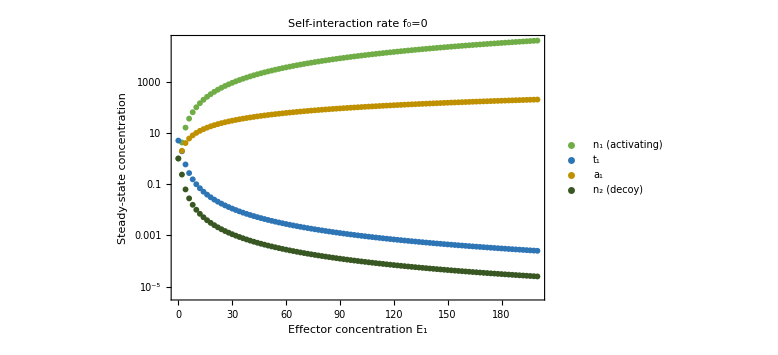

```mathematica
ListLogPlot[{r1Coords,tCoords,aCoords,r2Coords},PlotRange->{Automatic,Automatic},FrameLabel->{"Effector concentration E_1","Steady-state concentration"},LabelStyle->Directive[Black, 15],PlotLegends->{"n_1 (activating)","t_1","a_1","n_2 (decoy)"},Frame->{True,True,False,False},PlotLabel->"Self-interaction rate f_0="<>ToString[f0],ImageSize->Large,PlotStyle->colors]
```

```mathematica
(*Export["integratedDecoy_bifurcationPlot_f0_"<>ToString[f0]<>"_fi_"<>ToString[f1]<>".png",%,ImageResolution->200]*)
```

integratedDecoy_bifurcationPlot_f0_0_fi_1.png

```mathematica
(*Export["integratedDecoyPoints_f0_"<>ToString[f0]<>"_fi_"<>ToString[f1]<>"_n1tan2.mx",{r1Coords,tCoords,aCoords,r2Coords}];*)
```